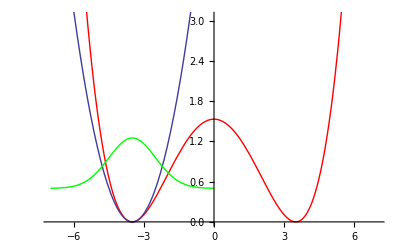

```mathematica
om=1;
d=7;
V=.5om^2(z^2-(d/2)^2)^2/d^2;
Vho1=.5om^2(z+d/2)^2;
DV1=V-Vho1;
phi1=(om/Pi)^(1/4)Exp[-om (z+d/2)^2/2];
gv=Plot[V,{z,-d,d},PlotStyle->Red];
gv1=Plot[V1,{z,-d,0}];
gphi1=Plot[phi1+om/2,{z,-d,0},PlotStyle->Green];
E01=om/2;
Show[gv,gv1,gphi1,PlotRange->{0,2Vb}]
```

```mathematica
(* Calc. of the lowest energy levels by diagonalizing Hmat in the single well basis (approx.) *)
V=om^2(z^2-(d/2)^2)^2/(2d^2);
Vho=om^2(z+d/2)^2/2;
DV=V-Vho;
nmax=10
Hmat=Table[0,{i,1,nmax+1},{j,1,nmax+1}];
Do[Do[m=i-1;n=j-1;
phiL=(om/Pi)^(1/4)Exp[-om (z+d/2)^2/2]HermiteH[m,Sqrt[om](z+d/2)]/Sqrt[2^m m!];
phiR=(om/Pi)^(1/4)Exp[-om (z+d/2)^2/2]HermiteH[n,Sqrt[om](z+d/2)]/Sqrt[2^n n!];
E0=om(n+1/2);
Vmn=NIntegrate[phiL DV phiR,{z,-Infinity,Infinity}];
Hmat[[i,j]]=Vmn+E0 KroneckerDelta[m,n],
{i,1,nmax+1}],{j,1,nmax+1}]
Ei =Sort[Eigenvalues[Hmat]]
```

10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.32161}. NIntegrate obtained 6.9389×10^-18 and 6.71174×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.32161}. NIntegrate obtained -1.30104×10^-18 and 8.81939×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.09582}. NIntegrate obtained -1.47451×10^-17 and 9.91156×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{0.477181,1.31046,1.91922,2.59842,3.50167,4.58285,5.8631,7.22766,8.84111,11.9794,19.0178}

```mathematica
(* Calc. of the lowest energy levels by diagonalizing Hmat in the double-well basis *)
V=om^2(z^2-(d/2)^2)^2/(2d^2);
z1=d/2+z;
z2=d/2-z;
Vho1=om^2z1^2/2;
Vho2=om^2z2^2/2;
DV1=V-Vho1;
DV2=V-Vho2;
nmax=10
Hmat=Table[0,{i,1,2nmax+2},{j,1,2nmax+2}];
Smat=Table[0,{i,1,2nmax+2},{j,1,2nmax+2}];
Do[n=j-1;
Do[m=i-1;
phi1L=(om/Pi)^(1/4)Exp[-om z1^2/2]HermiteH[m,Sqrt[om]z1]/Sqrt[2^m m!];
phi1R=(om/Pi)^(1/4)Exp[-om z1^2/2]HermiteH[n,Sqrt[om]z1]/Sqrt[2^n n!];
phi2L=(om/Pi)^(1/4)Exp[-om z2^2/2]HermiteH[m,Sqrt[om]z2]/Sqrt[2^m m!];
phi2R=(om/Pi)^(1/4)Exp[-om z2^2/2]HermiteH[n,Sqrt[om]z2]/Sqrt[2^n n!];
E0=om(n+1/2);
Vmn1=NIntegrate[phi1L DV1 phi1R,{z,-Infinity,Infinity}];
Vmn12=NIntegrate[phi1L DV2 phi2R,{z,-Infinity,Infinity}];
Vmn21=NIntegrate[phi2L DV1 phi1R,{z,-Infinity,Infinity}];
Vmn2=NIntegrate[phi2L DV2 phi2R,{z,-Infinity,Infinity}];
Smn1=KroneckerDelta[m,n];
Smn12=NIntegrate[phi1L phi2R,{z,-Infinity,Infinity}];
Smn21=NIntegrate[phi2L phi1R,{z,-Infinity,Infinity}];
Smn2=KroneckerDelta[m,n];
Hmat[[i,j]]=Vmn1+E0 KroneckerDelta[m,n] ;
Hmat[[i+nmax+1,j]]=Vmn21+E0 Smn21 ;
Hmat[[i,j+nmax+1]]=Vmn12+E0 Smn12 ;
Hmat[[i+nmax+1,j+nmax+1]]=Vmn2+E0 KroneckerDelta[m,n] ;
Smat[[i,j]]=Smn1;
Smat[[i+nmax+1,j]]=Smn21 ;
Smat[[i,j+nmax+1]]=Smn12 ;
Smat[[i+nmax+1,j+nmax+1]]=Smn2,
{i,1,nmax+1}],
{j,1,nmax+1}]
Ei =Sort[Eigenvalues[{Hmat,Smat}]]
```

10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.32161}. NIntegrate obtained 6.9389×10^-18 and 6.71174×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {5.32161}. NIntegrate obtained 6.9389×10^-18 and 6.71174×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.32161}. NIntegrate obtained -1.30104×10^-18 and 8.81939×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{0.476188,0.478131,1.26953,1.3514,1.83951,2.21861,2.71464,3.25469,3.84304,4.47114,5.13811,5.83644,6.58031,7.33511,8.12759,8.94123,9.81522,10.6615,12.8179,13.6075,19.9482,20.9086}

3

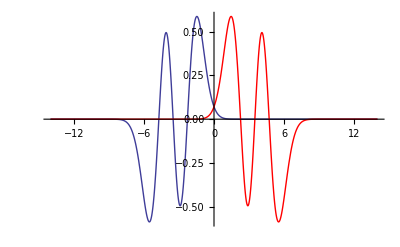

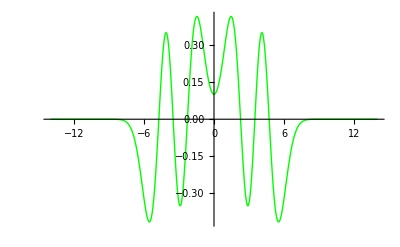

```mathematica
n=3
z1=d/2+z;
z2=d/2-z;
phi1=(om/Pi)^(1/4)Exp[-om z1^2/2]HermiteH[n,Sqrt[om]z1]/Sqrt[2^n n!];
phi2=(om/Pi)^(1/4)Exp[-om z2^2/2]HermiteH[n,Sqrt[om]z2]/Sqrt[2^n n!];
g1=Plot[phi1,{z,-2d,2d},PlotRange->All];
g2=Plot[phi2,{z,-2d,2d},PlotStyle->Red,PlotRange->All];
Show[g1,g2,PlotRange->All]
psi=(phi1+phi2)/Sqrt[2];
Plot[psi,{z,-2d,2d},PlotRange->All,PlotStyle->Green]
```

```mathematica
(* Calc. of the lowest energy levels by diagonalizing Hmat in the symmetrized double-well basis *)
V=om^2(z^2-(d/2)^2)^2/(2d^2);
z1=d/2+z;
z2=d/2-z;
Vho1=om^2z1^2/2;
Vho2=om^2z2^2/2;
DV1=V-Vho1;
DV2=V-Vho2;
nmax=10
Hmat=Table[0,{i,1,nmax+1},{j,1,nmax+1}];
Smat=Table[0,{i,1,nmax+1},{j,1,nmax+1}];
Do[n=j-1;
Do[m=i-1;
phi1L=(om/Pi)^(1/4)Exp[-om z1^2/2]HermiteH[m,Sqrt[om]z1]/Sqrt[2^m m!];
phi1R=(om/Pi)^(1/4)Exp[-om z1^2/2]HermiteH[n,Sqrt[om]z1]/Sqrt[2^n n!];
phi2L=(om/Pi)^(1/4)Exp[-om z2^2/2]HermiteH[m,Sqrt[om]z2]/Sqrt[2^m m!];
phi2R=(om/Pi)^(1/4)Exp[-om z2^2/2]HermiteH[n,Sqrt[om]z2]/Sqrt[2^n n!];
E0=om(n+1/2);
Vmn1=NIntegrate[phi1L DV1 phi1R,{z,-Infinity,Infinity}];
Vmn12=NIntegrate[phi1L DV2 phi2R,{z,-Infinity,Infinity}];
Vmn21=NIntegrate[phi2L DV1 phi1R,{z,-Infinity,Infinity}];
Vmn2=NIntegrate[phi2L DV2 phi2R,{z,-Infinity,Infinity}];
Smn1=KroneckerDelta[m,n];
Smn12=NIntegrate[phi1L phi2R,{z,-Infinity,Infinity}];
Smn21=NIntegrate[phi2L phi1R,{z,-Infinity,Infinity}];
Smn2=KroneckerDelta[m,n];
Smat[[i,j]]=Smn1+Smn21+Smn12+Smn2;
Hmat[[i,j]]=Vmn1+Vmn21+Vmn12+Vmn2+E0 Smat[[i,j]],
{i,1,nmax+1}],
{j,1,nmax+1}]
Ei =Eigenvalues[{Hmat,Smat}]
```

10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.32161}. NIntegrate obtained 6.9389×10^-18 and 6.71174×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {5.32161}. NIntegrate obtained 6.9389×10^-18 and 6.71174×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.32161}. NIntegrate obtained -1.30104×10^-18 and 8.81939×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{19.9482,12.8179,9.81522,8.12759,6.58031,5.13811,3.84304,2.71464,1.83951,1.26953,0.476188}

```mathematica
Eigenvectors[{Hmat,Smat}]
```

{{-0.0166373,-0.0495792,-0.0950126,-0.154405,-0.151171,-0.21115,0.041469,-0.190287,0.493886,-0.21399,0.75453},{0.0199287,0.0543969,0.126519,0.137961,0.296787,0.0102945,0.375862,-0.371652,0.12809,-0.347397,-0.675963},{0.0181609,0.0634518,0.0963592,0.237866,0.0970665,0.386677,-0.119947,0.206176,-0.0840944,-0.719806,-0.434453},{-0.014626,-0.0252788,-0.12387,-0.0125562,-0.339578,0.146584,-0.460801,-0.17787,0.597873,0.485122,0.100373},{0.00285771,0.0552835,-0.0365747,0.246326,-0.245611,0.607773,0.325679,-0.443181,-0.41478,-0.163582,-0.0627046},{0.0207631,-0.0373239,0.15566,-0.300742,0.694693,0.375661,-0.306164,-0.322039,-0.19524,-0.142824,-0.0617833},{0.0252917,-0.071937,0.308827,-0.771543,-0.328195,0.242582,0.251274,0.196377,0.163095,0.0893416,0.0262734},{-0.0190996,0.208018,-0.836895,-0.16844,0.266263,0.239209,0.21877,0.187118,0.114655,0.055563,0.0193681},{0.0320138,-0.664417,0.25948,0.44106,0.333851,0.300094,0.241015,0.158201,0.092895,0.046594,0.0152028},{0.187013,-0.785347,-0.446025,-0.247848,-0.216117,-0.156773,-0.101804,-0.0665058,-0.0383278,-0.0177792,-0.00567957},{0.983299,0.162717,0.0461451,0.0582717,0.0278165,0.0136735,0.0105506,0.00616164,0.00298327,0.00149725,0.000519991}}

```mathematica
(* Calc. of the lowest energy levels by diagonalizing Hmat in the antisymmetrized double-well basis *)
V=om^2(z^2-(d/2)^2)^2/(2d^2);
z1=d/2+z;
z2=d/2-z;
Vho1=om^2z1^2/2;
Vho2=om^2z2^2/2;
DV1=V-Vho1;
DV2=V-Vho2;
nmax=10
Hmat=Table[0,{i,1,nmax+1},{j,1,nmax+1}];
Smat=Table[0,{i,1,nmax+1},{j,1,nmax+1}];
Do[n=j-1;
Do[m=i-1;
phi1L=(om/Pi)^(1/4)Exp[-om z1^2/2]HermiteH[m,Sqrt[om]z1]/Sqrt[2^m m!];
phi1R=(om/Pi)^(1/4)Exp[-om z1^2/2]HermiteH[n,Sqrt[om]z1]/Sqrt[2^n n!];
phi2L=(om/Pi)^(1/4)Exp[-om z2^2/2]HermiteH[m,Sqrt[om]z2]/Sqrt[2^m m!];
phi2R=(om/Pi)^(1/4)Exp[-om z2^2/2]HermiteH[n,Sqrt[om]z2]/Sqrt[2^n n!];
E0=om(n+1/2);
Vmn1=NIntegrate[phi1L DV1 phi1R,{z,-Infinity,Infinity}];
Vmn12=NIntegrate[phi1L DV2 phi2R,{z,-Infinity,Infinity}];
Vmn21=NIntegrate[phi2L DV1 phi1R,{z,-Infinity,Infinity}];
Vmn2=NIntegrate[phi2L DV2 phi2R,{z,-Infinity,Infinity}];
Smn1=KroneckerDelta[m,n];
Smn12=NIntegrate[phi1L phi2R,{z,-Infinity,Infinity}];
Smn21=NIntegrate[phi2L phi1R,{z,-Infinity,Infinity}];
Smn2=KroneckerDelta[m,n];
Smat[[i,j]]=Smn1-Smn21-Smn12+Smn2;
Hmat[[i,j]]=Vmn1-Vmn21-Vmn12+Vmn2+E0 Smat[[i,j]],
{i,1,nmax+1}],
{j,1,nmax+1}]
Ei =Eigenvalues[{Hmat,Smat}]
```

10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.32161}. NIntegrate obtained 6.9389×10^-18 and 6.71174×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {5.32161}. NIntegrate obtained 6.9389×10^-18 and 6.71174×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.32161}. NIntegrate obtained -1.30104×10^-18 and 8.81939×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{20.9086,13.6075,10.6615,8.94123,7.33511,5.83644,4.47114,3.25469,2.21861,1.3514,0.478131}